```mathematica
Remove["Global`*"]
```

```mathematica
NormalDistribution[μ,σ]
```

NormalDistribution[μ,σ]

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

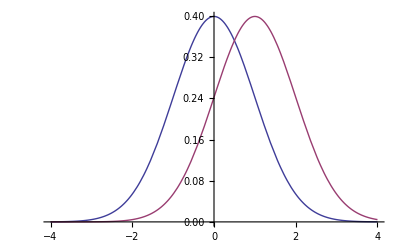

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[NormalDistribution[1,1],x]},{x,-4,4}]
```

```mathematica
PDF[NormalDistribution[μ,σ],x]/.x->μ
```

1/(√(2 π) σ)

```mathematica
Solve[PDF[NormalDistribution[μ,σ],x]==1/k*1/(√(2*Pi)*σ),x]
```

{{x→ConditionalExpression[μ-√2 σ √(2 ⅈ π C[1]+Log[k]),C[1]∈Integers]},{x→ConditionalExpression[μ+√2 σ √(2 ⅈ π C[1]+Log[k]),C[1]∈Integers]}}

```mathematica
Solve[PDF[NormalDistribution[μ,σ],x]==1/k*1/(√(2*Pi)*σ),x]/.C[1]->0
```

{{x→μ-√2 σ √Log[k]},{x→μ+√2 σ √Log[k]}}

```mathematica
Solve[PDF[NormalDistribution[μ,σ],x]==1/E*1/(√(2*Pi)*σ),x]/.C[1]->0
```

{{x→μ-√2 σ},{x→μ+√2 σ}}

```mathematica
(*E is e*)
```

```mathematica
Mean[NormalDistribution[μ,σ]]
```

μ

```mathematica
Assuming[σ>0,FullSimplify[Integrate[PDF[NormalDistribution[μ,σ],x],{x,-∞,∞}]]]
```

1

```mathematica
PDF[MaxwellDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3, x>0}, {0, True}}]

```mathematica
Assuming[σ>0,FullSimplify[Integrate[PDF[MaxwellDistribution[σ],x],{x,-∞,∞}]]]
```

1

```mathematica
PDF[PoissonDistribution[μ],k]
```

Piecewise[{{(ⅇ^-μ μ^k)/(k!), k≥0}, {0, True}}]

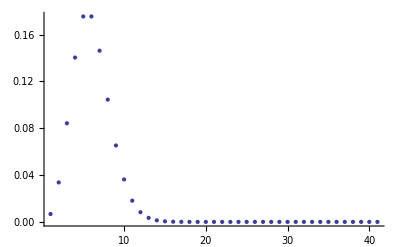

```mathematica
Show[
ListPlot[
Table[
PDF[PoissonDistribution[5],k],{k,0,40}]],PlotRange->All]
```

```mathematica
(*Random number generators*)
```

```mathematica
RandomReal[{0,1}]
```

0.563803

```mathematica
RandomVariate[NormalDistribution[0,1]]
```

-0.566598

```mathematica
data = RandomVariate[NormalDistribution[0,1],10^4]
```

{0.70644,-1.79282,-2.0725,-0.0668179,-0.256402,0.817285,«9989»,-0.700951,-0.223923,1.35159,0.868755,1.57564}

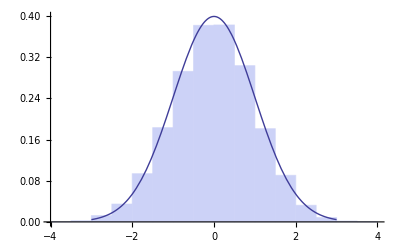

```mathematica
Show[Histogram[data,20,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}]]
```

```mathematica
(*the "ProbabilityDensity" option added in the end normalizes the histogram*)
```

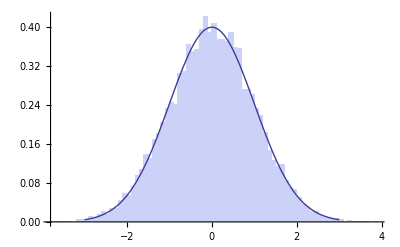

```mathematica
Show[Histogram[data,100,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}]]
```

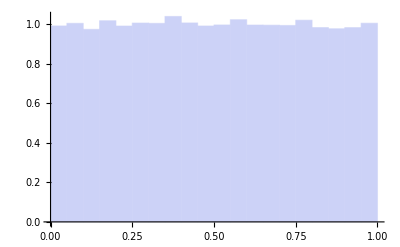

```mathematica
data2 = Table[RandomReal[{0,1}],{k,1,10^5}];
Histogram[data2,20,"ProbabilityDensity"]
```

```mathematica
X = {}
```

{}

```mathematica
AppendTo[X,2]
```

{2}

```mathematica
AppendTo[X,4]
AppendTo[X,6]
```

{2,4}

{2,4,6}

```mathematica
Q = {};
For[i=1,i<5000,i++,data3=Table[RandomReal[{0,1}],{k,1,1000}];m3=Mean[data3];AppendTo[Q,Mean[data3]]]
```

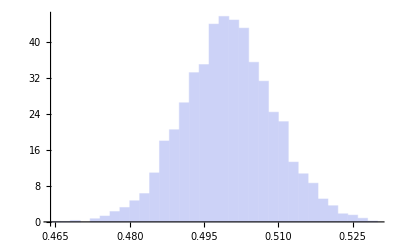

```mathematica
Histogram[Q,20,"ProbabilityDensity"]
```

```mathematica
Mean[Q]
```

0.499913

```mathematica
Variance[Q]
```

0.0000832517

Real[1/(20 √30)]

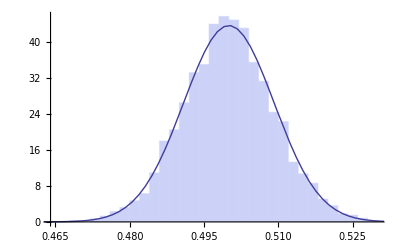

```mathematica
Show[Histogram[Q,20,"ProbabilityDensity"],Plot[PDF[NormalDistribution[1/2,√((1/12)/1000)],x],{x,-2,2}]]
```

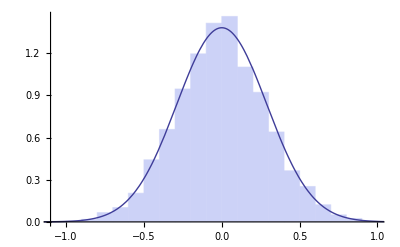

```mathematica
Show[Histogram[√1000*(Q-0.5),20,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,√(1/12)],x],{x,-2,2}]]
```

```mathematica
PDF[BinomialDistribution[N,p],n]
```

Piecewise[{{(1-p)^(-n+N) p^n Binomial[N,n], 0≤n≤N}, {0, True}}]

```mathematica
Mean[BinomialDistribution[N,p]]
```

N p

```mathematica
Variance[BinomialDistribution[N,p]]
```

N (1-p) p

```mathematica
Assuming[N>1,Sum[n*PDF[BinomialDistribution[N,p],n],{n,0,N}]]
```

N p

```mathematica
Assuming[N>1,Sum[n^2*PDF[BinomialDistribution[N,p],n],{n,0,N}]]
```

p (N-N p+N^2 p)

```mathematica
Assuming[N>1,Sum[(n-N*p)^2*PDF[BinomialDistribution[N,p],n],{n,0,N}]]
```

-N (-p+p^2)

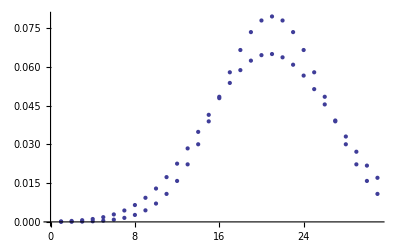

```mathematica
Show[ListPlot[Table[PDF[BinomialDistribution[100,1/2],n],{n,30,60}]],ListPlot[Table[PDF[BinomialDistribution[200,1/4],n],{n,30,60}]]
]
```

```mathematica
(*testing*)
```

```mathematica
ListPlot[CDF[NormalDistribution[0,1],x],{x,-1,1}]
```

ListPlot::nonopt: Options expected (instead of {x, -1, 1}) beyond position 3 in ListPlot[1/2\ Erfc[-x/√2], {x, -1, 1}]. An option must be a rule or a list of rules.

ListPlot[1/2 Erfc[-x/(√2)],{x,-1,1}]

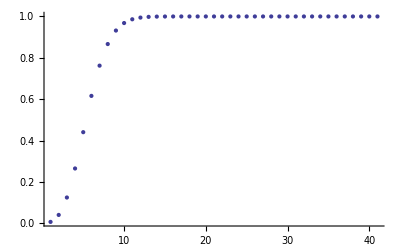

```mathematica
Show[
ListPlot[
Table[
CDF[PoissonDistribution[5],k],{k,0,40}]],PlotRange->All]
```